```mathematica
NPts=8*2^20
WFM1=Table[0.5*Cos[1.*2*π*(1*i)/NPts]+0.5*Cos[2*π*(100*i)/NPts],{i,NPts}];
MinMax[WFM1]
```

8388608

{-0.999753,1.}

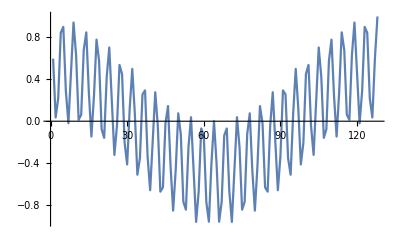

```mathematica
ListPlot[WFM1,Joined->True]
```

```mathematica
Export[NotebookDirectory[]<>"WFMTst8MPtsInt.txt",Map[ToString[Round[32767*#]]&,WFM1],"Table"]
```

C:\Data\_SoftDevelopment\AWG5200\WFMTst8MPtsInt.txt

```mathematica
Export[NotebookDirectory[]<>"WFMTst8MPts.txt",Map[ToString[NumberForm[#,6(*,ExponentFunction->(Null&)*),NumberFormat->(Row[{#1,If[#3=="","","E"],#3}]&)]]&,WFM1],"Table"]
```

C:\Data\LnepLab\Soft\Labview\AWG5200\WFMTst3.txt

```mathematica
NPts=2^24
WFM1=Table[0.5*Cos[1.*2*π*(1*i)/NPts]+0.5*Cos[2*π*(100*i)/NPts],{i,NPts}];
MinMax[WFM1]
```

16777216

{-0.999753,1.}

```mathematica
Export[NotebookDirectory[]<>"WFMTst16MPtsInt.txt",Map[ToString[Round[32767*#]]&,WFM1],"Table"]
```

C:\Data\_SoftDevelopment\AWG5200\WFMTst16MPtsInt.txt

```mathematica
Export[NotebookDirectory[]<>"WFMTst4.txt",Map[ToString[NumberForm[#,6(*,ExponentFunction->(Null&)*),NumberFormat->(Row[{#1,If[#3=="","","E"],#3}]&)]]&,WFM1],"Table"]
```

C:\Data\LnepLab\Soft\Labview\AWG5200\WFMTst4.txt

```mathematica
NPts=20000000
WFM1=Table[0.5*Cos[1.*2*π*(1*i)/NPts]+0.5*Cos[2*π*(100*i)/NPts],{i,NPts}];
MinMax[WFM1]
```

20000000

{-0.999753,1.}

```mathematica
Export[NotebookDirectory[]<>"WFMTst20E6PtsInt.txt",Map[ToString[Round[32767*#]]&,WFM1],"Table"]
```

C:\Data\_SoftDevelopment\AWG5200\WFMTst20E6PtsInt.txt

```mathematica
NPts=20000000
WFM1=Table[-32767,{i,NPts}];
WFM1[[Round[NPts/2.]]]=32767;
MinMax[WFM1]
ListPlot[WFM1]
```

20000000

{-32767,32767}

```mathematica
Export[NotebookDirectory[]<>"WFMTstSinglePixelPeak.txt",Map[ToString[#]&,WFM1],"Table"]
```

$Aborted